# Prepare

```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

```mathematica
Get["../../neuPackage/neutrino.wl"]
```

```mathematica
Get["../../neuPackage/neumat.wl"]
```

# Construct system

H=-ω_m/2 σ_3+H_1+H_2

```mathematica
hNList[{2,0},{0.5,0.95},{0.1,0.1},{0,0},0.197,x]
hNList[{0,1},{0.5,0.95},{0.1,0.1},{0,0},0.197,x]
```

{{0,0.000881578+0. ⅈ},{0.000881578+0. ⅈ,0}}

{{0,(0.+0.00950424 ⅈ) ⅇ^((0.-0.05 ⅈ) x)},{(0.-0.00950424 ⅈ) ⅇ^((0.+0.05 ⅈ) x),0}}

```mathematica
gamma1=0.00088;
gamma2=0.0095;
omega1=0+1;
omega2=-0.05+1;
initsys={psi1[0],psi2[0]}=={1,0};
endpointsys=10000;
```

```mathematica
hamilMeta[gamma_,omega_,omegam_:1]:=gamma{{0,Exp[I omega x]},{Exp[-I omega x],0}}
```

```mathematica
hamil1=hamilMeta[gamma1,omega1];
hamil2=I hamilMeta[gamma2,omega2];
```

```mathematica
hamilsys=-1/2 PauliMatrix[3]+hamil1+hamil2
```

{{-0.5+0. ⅈ,0.00088 ⅇ^(ⅈ x)+(0.+0.0095 ⅈ) ⅇ^((0.+0.95 ⅈ) x)},{0.00088 ⅇ^(-ⅈ x)+(0.+0.0095 ⅈ) ⅇ^((0.-0.95 ⅈ) x),0.5+0. ⅈ}}

```mathematica
solsys=NDSolve[I D[{psi1[x],psi2[x]},x]==hamilsys.{psi1[x],psi2[x]}&&initsys,{psi1,psi2},{x,0,endpointsys}]
```

{{psi1→InterpolatingFunction[{{0., 10000.}}, <>],psi2→InterpolatingFunction[{{0., 10000.}}, <>]}}

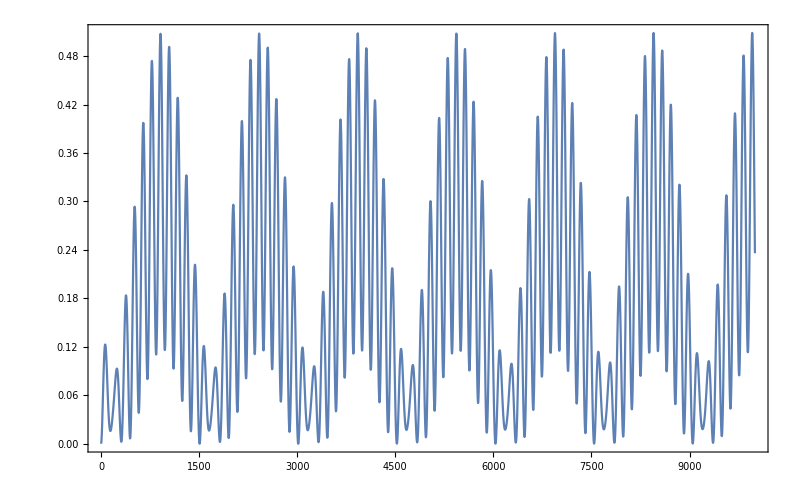

```mathematica
Plot[Evaluate[Abs[psi2[x]]^2/.First@solsys],{x,1,endpointsys},ImageSize->imgsize,Frame->True]
```

```mathematica
DSolve[I D[{psi1[x],psi2[x]},x]==hamil1.{psi1[x],psi2[x]},{psi1,psi2},x]
```

{{psi1→Function[{x},ⅇ^((0.-7.74399×10^-7 ⅈ) x) C[1]+ⅇ^((0.+1. ⅈ) x) C[2]],psi2→Function[{x},(0.000879999+0. ⅈ) ⅇ^((0.-1. ⅈ) x) C[1]-(1136.36+0. ⅈ) ⅇ^((0.+7.74399×10^-7 ⅈ) x) C[2]]}}